the rules of chess occupy 10 to the 5 pages in this language.

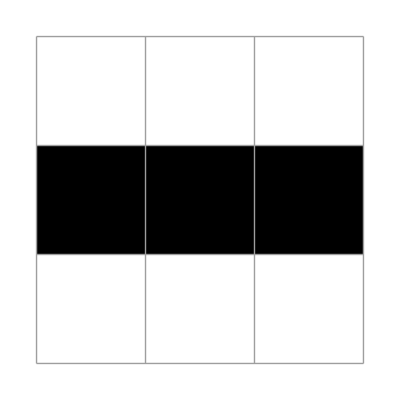
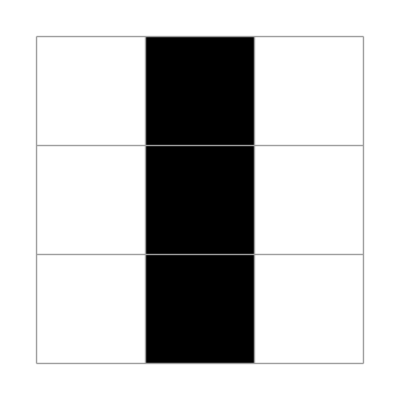

-Graphics-

```mathematica
X1=({{0, 0, 0}, {1, 1, 1}, {0, 0, 0}});
plt/@NestList[updateLife[{3,3}][ #]&,
X1,1]
```

```mathematica
Binomial[8,7]
```

8

```mathematica
Not/@Prepend[{1,2,3,4} ,xP]
```

{!xP,!1,!2,!3,!4}

## the 28

```mathematica
Clear[x];
lifeNeighbours={xNW,xN,xNE,xW,xE,xSW,xS,xSE};
lists28=(Prepend[Prepend[#,x],Not[xP]])&/@Subsets[lifeNeighbours,{6}];
the28=And@@Or@@@lists28
```

(!xP||x||xNW||xN||xNE||xW||xE||xSW)&&(!xP||x||xNW||xN||xNE||xW||xE||xS)&&(!xP||x||xNW||xN||xNE||xW||xE||xSE)&&(!xP||x||xNW||xN||xNE||xW||xSW||xS)&&(!xP||x||xNW||xN||xNE||xW||xSW||xSE)&&(!xP||x||xNW||xN||xNE||xW||xS||xSE)&&(!xP||x||xNW||xN||xNE||xE||xSW||xS)&&(!xP||x||xNW||xN||xNE||xE||xSW||xSE)&&(!xP||x||xNW||xN||xNE||xE||xS||xSE)&&(!xP||x||xNW||xN||xNE||xSW||xS||xSE)&&(!xP||x||xNW||xN||xW||xE||xSW||xS)&&(!xP||x||xNW||xN||xW||xE||xSW||xSE)&&(!xP||x||xNW||xN||xW||xE||xS||xSE)&&(!xP||x||xNW||xN||xW||xSW||xS||xSE)&&(!xP||x||xNW||xN||xE||xSW||xS||xSE)&&(!xP||x||xNW||xNE||xW||xE||xSW||xS)&&(!xP||x||xNW||xNE||xW||xE||xSW||xSE)&&(!xP||x||xNW||xNE||xW||xE||xS||xSE)&&(!xP||x||xNW||xNE||xW||xSW||xS||xSE)&&(!xP||x||xNW||xNE||xE||xSW||xS||xSE)&&(!xP||x||xNW||xW||xE||xSW||xS||xSE)&&(!xP||x||xN||xNE||xW||xE||xSW||xS)&&(!xP||x||xN||xNE||xW||xE||xSW||xSE)&&(!xP||x||xN||xNE||xW||xE||xS||xSE)&&(!xP||x||xN||xNE||xW||xSW||xS||xSE)&&(!xP||x||xN||xNE||xE||xSW||xS||xSE)&&(!xP||x||xN||xW||xE||xSW||xS||xSE)&&(!xP||x||xNE||xW||xE||xSW||xS||xSE)